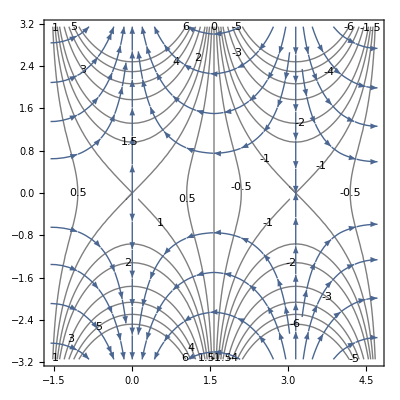

```mathematica
Show[
ContourPlot[Cos[x]Cosh[y],{x,-π/2,3π/2}, {y, -π,π},Contours->{0,0.5,1,1.5,2,3,4,5,6, -0.5,-1,-1.5,-2,-3,-4,-5,-6},MaxRecursion->2,ContourShading->None,ContourLabels->True],
StreamPlot[{-Sin[x]Cosh[y],Cos[x]Sinh[y]},{x,-π/2,3π/2}, {y, -π,π},
StreamPoints->Join[{{0,1},{0,-1},{π,1},{π,-1}},Flatten[Table[{x,y},{x,{-1,π/2,4}},{y,Complement[Range[-3,3,0.75],{0.}]}],1]]]]
```